# Load Files

```mathematica
SetDirectory[NotebookDirectory[]];

Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisP1.txt"}]];

(*LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_ptb,Infinity];*)
```

# Generate Phase-Space Point

```mathematica
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]

(*SubReduList=Get[ToString[StringForm["/home/dschiebe/Documents/lanayru/PhD_Files/PentaBoxImportingPureInts/KIRA/splitres/phasespace_00001.m",IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]]

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];*)


epsrepl={(ep->(4-d)/2)/.tPoint};
PureIntegralN=Expand[PureIntegrals/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
diffOp=getDifferentialOperator[tPoint];
checkDifferentialOperator[tPoint,diffOp]
```

{d→1095796003,mt2→783259337,s12→497087249,s123→45334335,s16→1036540855,s23→241739091,s234→852477217,s34→293661823,s345→850852145,s45→1744075771,s56→1326677154}

0.206376

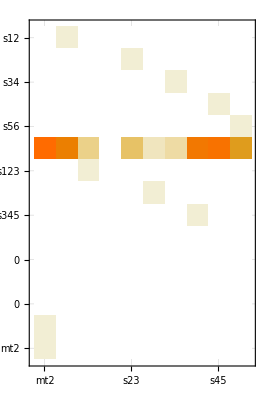

Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

«7 more identical outputs»

# Compute Basis Change Matrix

102

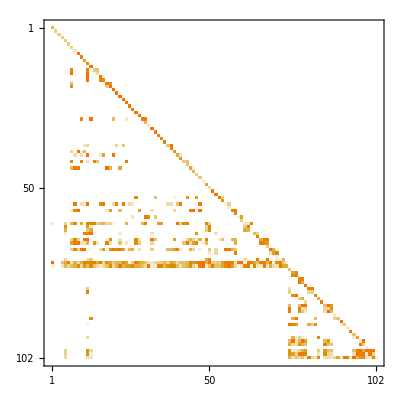

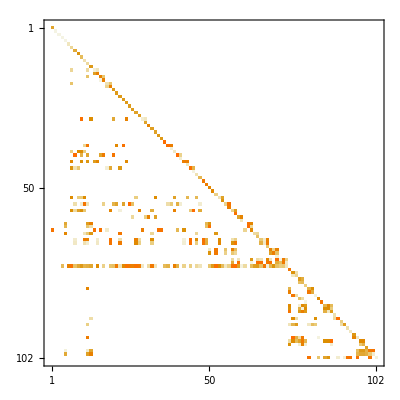

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;

PureIntegralN4=Expand[PureIntegralN4/.epsrepl,Modulus->$P];

BasisChangMat=Table[CoefficientArrays[PureIntegralN4[[pos]],SubLaporta],{pos,1,Length[PureIntegralN]}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
BasisChangMatInv//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
DeleteList=Delete[{1,2,3,4,5,6,7,8,9,10,11},Position[tPoint[[All,1]],s16]];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[DeleteCases[DeleteList,var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],Row[{ProgressIndicator[(var-1)*102+intpos,{1,102*10}],"  ",var,"/10 ",intpos,"/102"}]];
```

## Extra Step If Redu List does not exit yet

```mathematica
ToReduce=Cases[diffInts,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];

ToReduce2=Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];

GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ExtraRelationsReduList.txt"}]];

DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
WriteJobFile[{"ExtraRelationsReduList","UReduList","ReduList"}]
```

6198

587

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules/.ExtraRelations,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,SubLaporta];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

344

# Compute DE Matrices

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],SubLaporta]/.{0}->{0,ConstantArray[0,102]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[SubLaporta]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
Mplot5=MatrixPlot[Expand[dhxbMatrices[[5]].BasisChangMatInv,Modulus->$P]];
Mplot6=MatrixPlot[Expand[dhxbMatrices[[6]].BasisChangMatInv,Modulus->$P]];
Mplot7=MatrixPlot[Expand[dhxbMatrices[[7]].BasisChangMatInv,Modulus->$P]];
Mplot8=MatrixPlot[Expand[dhxbMatrices[[8]].BasisChangMatInv,Modulus->$P]];
Mplot9=MatrixPlot[Expand[dhxbMatrices[[9]].BasisChangMatInv,Modulus->$P]];
Mplot10=MatrixPlot[Expand[dhxbMatrices[[10]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2,Mplot3,Mplot4,Mplot5},{Mplot6,Mplot7,Mplot8,Mplot9,Mplot10}}]
```

-Graphics-

(2 ep hxb[1,0,0,1,1,0,0,0,0,0,0,0,0])/s12-(13 ep^2 hxb[1,0,0,1,1,0,0,0,0,0,0,0,0])/s12+(27 ep^3 hxb[1,0,0,1,1,0,0,0,0,0,0,0,0])/s12-(18 ep^4 hxb[1,0,0,1,1,0,0,0,0,0,0,0,0])/s12

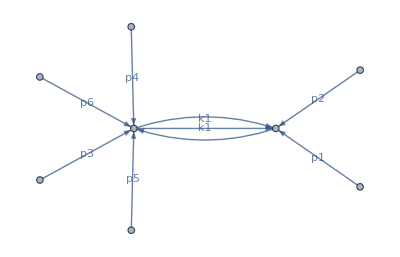

```mathematica
PureIntegrals[[2]]
 plotDiagram[hxb[1,0,0,1,1,0,0,0,0,0,0,0,0]]
```

ep^3 hxb[1,0,0,2,1,0,0,1,0,0,0,0,0] root[-4 mt2 s12+(-mt2-s12+s345)^2]

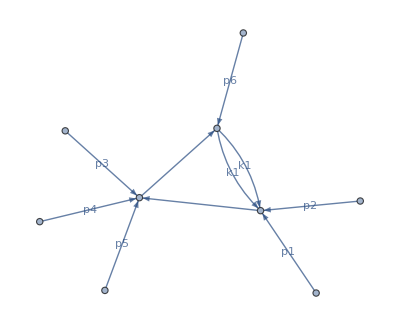

```mathematica
PureIntegrals[[8]]
 plotDiagram[hxb[1,0,0,2,1,0,0,1,0,0,0,0,0]]
```

```mathematica
Expand[applyDifferentialOperator[Coefficient[diffOp,ds[S23]],SixPointGram]/.tPoint,Modulus->$P]
```

0

345281253 del[s12]+del[s23]+1507816084 del[p[1]] p[1]+1040533602 del[p[5]] p[1]+1746617608 del[p[6]] p[1]+868569090 del[p[1]] p[2]+852687611 del[p[2]] p[2]+777796915 del[p[4]] p[2]+909091129 del[p[5]] p[2]+886822549 del[p[6]] p[2]+1019243367 del[p[1]] p[3]+225894583 del[p[4]] p[3]+1367397607 del[p[5]] p[3]+1682431737 del[p[6]] p[3]+210298977 del[p[1]] p[4]+1308985951 del[p[4]] p[4]+281459597 del[p[5]] p[4]+346739122 del[p[6]] p[4]

```mathematica
loopMomentumScalarProducts=Get[FileNameJoin[{Directory[],"files/loopmomentum_scalarproducts.txt"}]];
	momenta={p[1],p[2],p[3],p[4],p[5]};
	SixPointGram=Expand[Det[Table[momenta[[i]] momenta[[j]],{i,1,5},{j,1,5}]/.kinematics/.mandelstamScalarProducts/.loopMomentumScalarProducts]];
```

```mathematica
diffOp=getDifferentialOperator[tPoint];
```

{ds[S12]→237655615 ds[Mt2]+1644123478 ds[S123]+184364507 ds[S16]+345281253 ds[S23]+734846478 ds[S234]+1977253653 ds[S34]+1868325316 ds[S345]+1862462919 ds[S45]+1210124516 ds[S56],da[4,6]→1049721975 ds[Mt2]+1650362341 ds[S123]+1446785568 ds[S16]+346739122 ds[S23]+343355644 ds[S234]+1277747019 ds[S34]+925197756 ds[S345]+1875740308 ds[S45]+1968860263 ds[S56],da[3,6]→1828606009 ds[Mt2]+1076024897 ds[S123]+1689436808 ds[S16]+1682431737 ds[S23]+782883056 ds[S234]+280726343 ds[S34]+1295128544 ds[S345]+1273090339 ds[S45]+776096916 ds[S56],da[2,6]→119955673 ds[Mt2]+2068300917 ds[S123]+1299116122 ds[S16]+886822549 ds[S23]+649484969 ds[S234]+609624539 ds[S34]+1712857257 ds[S345]+1447310561 ds[S45]+384441006 ds[S56],da[1,6]→291713651 ds[Mt2]+511300241 ds[S123]+521831074 ds[S16]+1746617608 ds[S23]+1639755948 ds[S234]+116297855 ds[S34]+1011738557 ds[S345]+553270763 ds[S45]+1837082484 ds[S56],da[1,1]→1210561148 ds[Mt2]+1636183406 ds[S123]+1718785809 ds[S16]+1507816084 ds[S23]+62401691 ds[S234]+333018604 ds[S34]+1119418127 ds[S345]+835633604 ds[S45]+310401163 ds[S56],da[4,5]→1237794702 ds[Mt2]+1408434122 ds[S16]+281459597 ds[S23]+1969298376 ds[S234]+654755321 ds[S34]+429828519 ds[S345]+1086766864 ds[S45],da[3,5]→891836285 ds[Mt2]+992268760 ds[S16]+1367397607 ds[S23]+188604479 ds[S234]+1628521397 ds[S34]+220232153 ds[S345]+1821445777 ds[S45],da[2,5]→185651343 ds[Mt2]+1444013306 ds[S16]+909091129 ds[S23]+7003696 ds[S234]+1193167731 ds[S34]+2064818710 ds[S345]+1259365136 ds[S45],da[1,5]→645208848 ds[Mt2]+2054350411 ds[S16]+1040533602 ds[S23]+445326008 ds[S234]+1698167188 ds[S34]+16326963 ds[S345]+758579280 ds[S45],da[4,4]→1308985951 ds[S23]+1485895714 ds[S234]+1108280101 ds[S34],da[4,1]→2007450617 ds[Mt2]+497121306 ds[S123]+1439747604 ds[S16]+210298977 ds[S23]+496417560 ds[S234]+1254184853 ds[S34]+792457372 ds[S345]+1332460122 ds[S45]+178623384 ds[S56],da[3,1]→1574525000 ds[Mt2]+1071458750 ds[S123]+1613261726 ds[S16]+1019243367 ds[S23]+1823394130 ds[S234]+1602382259 ds[S34]+632122950 ds[S345]+1200431178 ds[S45]+1371386731 ds[S56],da[2,2]→852687611 ds[S23],da[2,1]→1841876631 ds[Mt2]+79182730 ds[S123]+1551837866 ds[S16]+868569090 ds[S23]+1972007801 ds[S234]+511076576 ds[S34]+517291327 ds[S345]+1588291597 ds[S45]+1763042641 ds[S56],da[3,4]→225894583 ds[S23]+1500085629 ds[S234]+783337295 ds[S34],da[2,4]→777796915 ds[S23]+1666470828 ds[S234]+1981098448 ds[S34],da[4,2]→0,da[4,3]→0,da[1,2]→0,da[1,3]→0,da[1,4]→0,da[2,3]→0,da[3,2]→0,da[3,3]→0}

```mathematica
ds12={ds[S12]->237655615 ds[Mt2]+1644123478 ds[S123]+184364507 ds[S16]+345281253 ds[S23]+734846478 ds[S234]+1977253653 ds[S34]+1868325316 ds[S345]+1862462919 ds[S45]+1210124516 ds[S56]}
```

{ds[S12]→237655615 ds[Mt2]+1644123478 ds[S123]+184364507 ds[S16]+345281253 ds[S23]+734846478 ds[S234]+1977253653 ds[S34]+1868325316 ds[S345]+1862462919 ds[S45]+1210124516 ds[S56]}

```mathematica
ds12[[1,2]]
```

237655615 ds[Mt2]+1644123478 ds[S123]+184364507 ds[S16]+345281253 ds[S23]+734846478 ds[S234]+1977253653 ds[S34]+1868325316 ds[S345]+1862462919 ds[S45]+1210124516 ds[S56]

```mathematica
Expand[Total[Table[applyDifferentialOperator[Coefficient[diffOp,ds[invariantsnodUpperCase[[i]]]],s12]Coefficient[ds12[[1,2]],ds[invariantsnodUpperCase[[i]]]],{i,1,10}]],Modulus->$P]
```

1490563165

```mathematica
Expand[applyDifferentialOperator[diffOp,s12],Modulus->$P]
```

```mathematica
ds16=Solve[ds12[[1,2]]==ds[S12],ds[S16],Modulus->$P][[1]]
```

{ds[S16]→926905306 ds[Mt2]+135581157 ds[S12]+2119887156 ds[S123]+2051446438 ds[S23]+2014329633 ds[S234]+2125705614 ds[S34]+498776063 ds[S345]+124434458 ds[S45]+804695630 ds[S56]}

```mathematica
diffOps16=Expand[diffOp/.ds16];
```

```mathematica
Expand[applyDifferentialOperator[diffOps16,s23],Modulus->$P]
Expand[applyDifferentialOperator[diffOp,s23],Modulus->$P]
```

ds[S23]

ds[S23]

{1,2,3,4,6,7,8,9,10,11}

```mathematica
invariants[[All,1]]
```

Part::partd: Part specification {d,mt2,s12,s123,s16,s23,s234,s34,s345,s45,«1»}⟦All,1⟧ is longer than depth of object.

{d,mt2,s12,s123,s16,s23,s234,s34,s345,s45,s56}⟦All,1⟧

```mathematica
DeleteList
DeleteCases[DeleteList,4+1]
```

{1,2,3,4,6,7,8,9,10,11}

{1,2,3,4,6,7,8,9,10,11}

```mathematica
DeleteCases[{a,b,c,d},b]
```

{a,c,d}